```mathematica
4
```

```mathematica
P = {{pi0 + c*kb, pi1 - c*kb}, {pi0 - ku, pi1 + ku}}
```

{{c kb+ku/(c kb+ku),-c kb+(c kb)/(c kb+ku)},{-ku+ku/(c kb+ku),ku+(c kb)/(c kb+ku)}}

```mathematica
MatrixForm[P]
```

(c kb+ku/(c kb+ku) | -c kb+(c kb)/(c kb+ku)
-ku+ku/(c kb+ku) | ku+(c kb)/(c kb+ku))

```mathematica
Inverse[P]
```

{{(ku+(c kb)/(c kb+ku))/((c^2 kb^2)/(c kb+ku)+(2 c kb ku)/(c kb+ku)+ku^2/(c kb+ku)),(c kb-(c kb)/(c kb+ku))/((c^2 kb^2)/(c kb+ku)+(2 c kb ku)/(c kb+ku)+ku^2/(c kb+ku))},{(ku-ku/(c kb+ku))/((c^2 kb^2)/(c kb+ku)+(2 c kb ku)/(c kb+ku)+ku^2/(c kb+ku)),(c kb+ku/(c kb+ku))/((c^2 kb^2)/(c kb+ku)+(2 c kb ku)/(c kb+ku)+ku^2/(c kb+ku))}}

```mathematica
P' = Inverse[P] - {{pi0, pi1}, {pi0, pi1}}
```

{{-ku/(c kb+ku)+(ku+(c kb)/(c kb+ku))/((c^2 kb^2)/(c kb+ku)+(2 c kb ku)/(c kb+ku)+ku^2/(c kb+ku)),-(c kb)/(c kb+ku)+(c kb-(c kb)/(c kb+ku))/((c^2 kb^2)/(c kb+ku)+(2 c kb ku)/(c kb+ku)+ku^2/(c kb+ku))},{-ku/(c kb+ku)+(ku-ku/(c kb+ku))/((c^2 kb^2)/(c kb+ku)+(2 c kb ku)/(c kb+ku)+ku^2/(c kb+ku)),-(c kb)/(c kb+ku)+(c kb+ku/(c kb+ku))/((c^2 kb^2)/(c kb+ku)+(2 c kb ku)/(c kb+ku)+ku^2/(c kb+ku))}}

```mathematica
Z = Simplify[P', {pi0 = ku / (ku + c*kb), pi1 = c*kb / (ku + c*kb)}]
```

{{(c kb)/(c kb+ku)^2,-(c kb)/(c kb+ku)^2},{-ku/(c kb+ku)^2,ku/(c kb+ku)^2}}

```mathematica
Q = {{-(kui_a+kui_b),kui_a,kui_b,0},{kua_i,-(kua_i+kua_b),0,kua_b},{kbi_u,0,-(kbi_u+kbi_a),kbi_a},{0,kba_u,kba_i,-(kba_u+kba_i)}}
```

{{-kui_a-kui_b,kui_a,kui_b,0},{kua_i,-kua_b-kua_i,0,kua_b},{kbi_u,0,-kbi_a-kbi_u,kbi_a},{0,kba_u,kba_i,-kba_i-kba_u}}

```mathematica
Q' = Transpose[{{-(kui_a+c*kui_b),kui_a,c*kui_b,1},{kua_i,-(kua_i+c*kua_b),0,1},{kbi_u,0,-(kbi_u+kbi_a),1},{0,kba_u,kba_i,1}}]
```

{{-kui_a-c kui_b,kua_i,kbi_u,0},{kui_a,-c kua_b-kua_i,0,kba_u},{c kui_b,0,-kbi_a-kbi_u,kba_i},{1,1,1,1}}

```mathematica
LinearSolve[Q', {0,0,0,1}]
```

{(c kba_i kbi_u kua_b+kba_u kbi_a kua_i+kba_i kbi_u kua_i+kba_u kbi_u kua_i)/(c kba_i kbi_u kua_b+kba_u kbi_a kua_i+kba_i kbi_u kua_i+kba_u kbi_u kua_i+kba_u kbi_a kui_a+kba_i kbi_u kui_a+kba_u kbi_u kui_a+c kba_i kua_b kui_a+c kbi_a kua_b kui_a+c kbi_u kua_b kui_a+c kba_u kbi_a kui_b+c^2 kba_i kua_b kui_b+c^2 kbi_a kua_b kui_b+c kba_i kua_i kui_b+c kba_u kua_i kui_b+c kbi_a kua_i kui_b),(kba_u kbi_a kui_a+kba_i kbi_u kui_a+kba_u kbi_u kui_a+c kba_u kbi_a kui_b)/(c kba_i kbi_u kua_b+kba_u kbi_a kua_i+kba_i kbi_u kua_i+kba_u kbi_u kua_i+kba_u kbi_a kui_a+kba_i kbi_u kui_a+kba_u kbi_u kui_a+c kba_i kua_b kui_a+c kbi_a kua_b kui_a+c kbi_u kua_b kui_a+c kba_u kbi_a kui_b+c^2 kba_i kua_b kui_b+c^2 kbi_a kua_b kui_b+c kba_i kua_i kui_b+c kba_u kua_i kui_b+c kbi_a kua_i kui_b),(c kba_i kua_b kui_a+c^2 kba_i kua_b kui_b+c kba_i kua_i kui_b+c kba_u kua_i kui_b)/(c kba_i kbi_u kua_b+kba_u kbi_a kua_i+kba_i kbi_u kua_i+kba_u kbi_u kua_i+kba_u kbi_a kui_a+kba_i kbi_u kui_a+kba_u kbi_u kui_a+c kba_i kua_b kui_a+c kbi_a kua_b kui_a+c kbi_u kua_b kui_a+c kba_u kbi_a kui_b+c^2 kba_i kua_b kui_b+c^2 kbi_a kua_b kui_b+c kba_i kua_i kui_b+c kba_u kua_i kui_b+c kbi_a kua_i kui_b),(c (kbi_a kua_b kui_a+kbi_u kua_b kui_a+c kbi_a kua_b kui_b+kbi_a kua_i kui_b))/(c kba_i kbi_u kua_b+kba_u kbi_a kua_i+kba_i kbi_u kua_i+kba_u kbi_u kua_i+kba_u kbi_a kui_a+kba_i kbi_u kui_a+kba_u kbi_u kui_a+c kba_i kua_b kui_a+c kbi_a kua_b kui_a+c kbi_u kua_b kui_a+c kba_u kbi_a kui_b+c^2 kba_i kua_b kui_b+c^2 kbi_a kua_b kui_b+c kba_i kua_i kui_b+c kba_u kua_i kui_b+c kbi_a kua_i kui_b)}

```mathematica
FullSimplify[%]
```

{(kba_u (kbi_a+kbi_u) kua_i+kba_i kbi_u (c kua_b+kua_i))/((kbi_a+kbi_u) (c kua_b kui_a+kba_u (kua_i+kui_a))+c (kba_u (kbi_a+kua_i)+kbi_a (c kua_b+kua_i)) kui_b+kba_i (c kua_b kui_a+kbi_u (c kua_b+kua_i+kui_a)+c (c kua_b+kua_i) kui_b)),(kba_i kbi_u kui_a+kba_u ((kbi_a+kbi_u) kui_a+c kbi_a kui_b))/((kbi_a+kbi_u) (c kua_b kui_a+kba_u (kua_i+kui_a))+c (kba_u (kbi_a+kua_i)+kbi_a (c kua_b+kua_i)) kui_b+kba_i (c kua_b kui_a+kbi_u (c kua_b+kua_i+kui_a)+c (c kua_b+kua_i) kui_b)),(c kba_i kua_b kui_a+c (c kba_i kua_b+(kba_i+kba_u) kua_i) kui_b)/((kbi_a+kbi_u) (c kua_b kui_a+kba_u (kua_i+kui_a))+c (kba_u (kbi_a+kua_i)+kbi_a (c kua_b+kua_i)) kui_b+kba_i (c kua_b kui_a+kbi_u (c kua_b+kua_i+kui_a)+c (c kua_b+kua_i) kui_b)),(c (kbi_a+kbi_u) kua_b kui_a+c kbi_a (c kua_b+kua_i) kui_b)/((kbi_a+kbi_u) (c kua_b kui_a+kba_u (kua_i+kui_a))+c (kba_u (kbi_a+kua_i)+kbi_a (c kua_b+kua_i)) kui_b+kba_i (c kua_b kui_a+kbi_u (c kua_b+kua_i+kui_a)+c (c kua_b+kua_i) kui_b))}

```mathematica
Q = {{-c*kb, c*kb}, {ku, -ku}}
```

{{-c kb,c kb},{ku,-ku}}

```mathematica
Eigensystem[Q]
```

{{0,-c kb-ku},{{1,1},{-(c kb)/ku,1}}}

```mathematica
{d = DiagonalMatrix[First[%]], p = Transpose[Last[%]]}
```

{{{0,0},{0,-c kb-ku}},{{1,-(c kb)/ku},{1,1}}}

```mathematica
Q == FullSimplify[p.d.Inverse[p]]
```

True

```mathematica
Q == FullSimplify[p.d.Inverse[p]]
```

True

```mathematica
P = MatrixExp[t*Q]
```

{{(c ⅇ^((-c kb-ku) t) kb)/(c kb+ku)+ku/(c kb+ku),(c kb)/(c kb+ku)-(c ⅇ^((-c kb-ku) t) kb)/(c kb+ku)},{ku/(c kb+ku)-(ⅇ^((-c kb-ku) t) ku)/(c kb+ku),(c kb)/(c kb+ku)+(ⅇ^((-c kb-ku) t) ku)/(c kb+ku)}}

```mathematica
Qoff = {{0,0}, {ku,-ku}};
Poff = MatrixExp[t*Qoff];
Fpt = Dot[Qoff, Poff]
```

{{0,0},{ku-ⅇ^(-ku t) (-1+ⅇ^(ku t)) ku,-ⅇ^(-ku t) ku}}

```mathematica
FullSimplify[Fpt]
```

{{0,0},{ⅇ^(-ku t) ku,-ⅇ^(-ku t) ku}}

```mathematica
(* Computing the IR_acc algebraically in limiting circuits *)
```

```mathematica
Q3 = {{-c*kb,0, c*kb},{0, -kon, kon},{ku, koff, -(ku+koff)}};
Q3b = {{-c*kb,0, c*kb},{0, -koff, koff},{ku, kon, -(ku+kon)}};
Q3c = {{-ku,0, ku},{0, -koff, koff},{c*kb, kon, -(c*kb+kon)}};
Q3d = {{-ku,0, ku},{0, -kon, kon},{c*kb, koff, -(c*kb+koff)}};
Q4acc = {{-(c*kboff+konu),konu,c*kboff,0},
             {koffu,-(koffu+c*kbon),0,c*kbon},
             {kuoff,0,-(konb+kuoff),konb}, 
             {0,kuon,koffb,-(kuon+koffb)}};
Q4opt = {{-(c*kboff),0,c*kboff,0},
             {koffu,-(koffu+c*kbon),0,c*kbon},
             {0,0,-(konb),konb}, 
             {0,kuon,0,-(kuon)}};
Q4T = {{-(c*kb),0,c*kb,0},
             {ky,-(ky),0,0},
             {ku,kx,-(koff+ku+kx),koff}, 
             {0,kon,0,-(kon)}};
Q4M = {{-(c*kb+koff),koff,c*kb,0},
             {kon,-(kon+c*kb),0,c*kb},
             {ku,0,-(koff/m+ku),koff/m}, 
             {0,ku,kon*m,-(ku+kon*m)}};
M4acc = MatrixForm[Q4acc]
```

(-c kboff-konu | konu | c kboff | 0
koffu | -c kbon-koffu | 0 | c kbon
kuoff | 0 | -konb-kuoff | konb
0 | kuon | koffb | -koffb-kuon)

```mathematica
Q = Q4opt;
R = Q; R[[All, -1]] = 1;
RT = Transpose[R];
pss = LinearSolve[RT, {0,0,0,1}];
pion = pss[[2]] + pss[[4]];
pib =  pss[[3]]+pss[[4]];
dpion = D[pion, c];
s = FullSimplify[c * dpion];
Pss = {pss, pss, pss,pss};
Z = Inverse[Pss - Q] - Pss;
var = 2*(pss[[2]]*Z[[2,2]] + pss[[2]]*Z[[2,4]] + pss[[4]]*Z[[4,2]] + pss[[4]]*Z[[4,4]]);
IR = 0.5 * (dc/c)^2* s^2 / var;
mfpt41 = (Z[[1,1]] - Z[[4,1]]) / pss[[1]];
```

```mathematica
FullSimplify[mfpt41]
```

(c kbon+koffu+kuon)/(koffu kuon)

```mathematica
S = s / (pion * (1 - pion));
S = FullSimplify[S]
```

konb/(c kboff+konb)+(c kbon)/(c kbon+koffu+kuon)

```mathematica
FullSimplify[With[{dc = c/10,konb = l, kuon=l,koffu=l}, Evaluate[s]]]
```

(c kboff l (c^2 kboff kbon+2 c kbon l+2 l^2))/((c^2 kboff kbon+3 c kboff l+l^2)^2)

```mathematica
FullSimplify[pion]
```

(c kboff konb (c kbon+koffu+kuon))/(c kboff (c kbon+koffu) konb+koffu konb kuon+c kboff (koffu+konb) kuon)

```mathematica
Var = var / (pion * (1 - pion))^2;
FullSimplify[FullSimplify[With[{dc = c/10,konb = l, kuon=l,koffu=l}, Evaluate[var]]]]
```

(2 c kboff (c^4 kboff^2 kbon^2+c^3 kboff kbon (4 kboff+kbon) l+c^2 (kboff+kbon) (3 kboff+kbon) l^2+2 c (kboff+2 kbon) l^3+3 l^4))/(c^2 kboff kbon+3 c kboff l+l^2)^3

```mathematica
IR=0.5*(dc/c)^2*s^2/var;
IRl = FullSimplify[With[{dc = c/10,konb = l, kuon=l,koffu=l}, Evaluate[IR]]]
```

(0.0025 c kboff l^2 (c^2 kboff kbon+2. c kbon l+2. l^2)^2)/((c^2 kboff kbon+3. c kboff l+l^2) (c^4 kboff^2 kbon^2+c^3 kboff kbon (4. kboff+kbon) l+c^2 (3. kboff^2+4. kboff kbon+kbon^2) l^2+c (2. kboff+4. kbon) l^3+3. l^4))

```mathematica
Maximize[{IR, konu<5, koffu<5, kuoff<5, kuon<5,kbon<=0.0888,kboff<=0.0888, c>=0},kbon]
```

$Aborted

```mathematica
IRcdc = With[{c =10^4, dc=10^3}, Evaluate[IR]];
```

```mathematica
NMaximize[{IRcdc, 10^-5<kbon < 0.0888, 10^-5<kboff < 0.0888, 10^-5<koffu<50, 10^-5<konb<5, 10^-5<kuon<5}, {kbon, kboff, koffu, konb, kuon}]
```

{2.95839×10^-6,{kbon→0.0834439,kboff→0.0888,koffu→4.99724,konb→4.93958,kuon→5.}}

```mathematica
NMaximize[{IRcdc, 10^-5<kbon < 0.0888, 10^-5<kboff < 0.0888, 10^-5<koffu<5,10^-5<kuoff<5,10^-5<konu<5,10^-5<koffb<5, 10^-5<konb<5, 10^-5<kuon<5}, {kbon, kboff, koffu, konb, kuon,kuoff,konu,koffb}]
```

```mathematica
With[{ kbon=0,kboff=1,koffu=5.,konb=5.,kuon=5.}, Evaluate[200*IRcdc/(10^-2*1)]]
```

0.661805

```mathematica
With[{c =10^4, kbon=0.0012293348624703138,kboff=0.0002526849063494677,koffu=5.,konb=5.,kuon=5.}, Evaluate[IRcdc]]
```

0.0034183

```mathematica
With[{c =10^-2, kbon = 0.0888, kboff=0.0888, koffu=5, konb=5, kuon=5}, Evaluate[S]]
```

0.999911

```mathematica
tau = (koffu + c*kbon)/(koffu*kuon) + 1/(c*kbon+koffu);
FullSimplify[1/tau]
```

(koffu (c kbon+koffu) kuon)/((c kbon+koffu)^2+koffu kuon)

```mathematica
Sc = With[{c =10^0}, Evaluate[S]];
NMaximize[{Sc, 10^-5<kbon < 0.0888, 10^-5<kboff < 0.0888, 10^-5<koffu<5, 10^-5<konb<5, 10^-5<kuon<5}, {kbon, kboff, koffu, konb, kuon}]
```

{1.99977,{kbon→0.0888,kboff→0.00001,koffu→0.00001,konb→5.,kuon→0.00001}}

```mathematica
FullSimplify[With[{kbon=0}, Evaluate[var]]]
```

(2 koffu (konu (koffb kuoff+(konb+kuoff) kuon)^3+c^2 kboff^2 (koffb (2 koffu^2 konb+koffb^2 konu) kuoff+(koffu^2 konb (konb+2 kuoff)+koffb koffu konb (-konb+konu+2 kuoff)+koffb^2 (3 konu kuoff+2 konb (konu+kuoff))) kuon+(koffu konb (konu+2 kuoff)+koffb (konb^2+3 konu kuoff+4 konb (konu+kuoff))) kuon^2+(konb^2+konu kuoff+2 konb (konu+kuoff)) kuon^3)+c^3 kboff^3 konb (koffb+kuon) (koffu^2+koffu kuon+kuon (koffb+kuon))+c kboff (koffb kuoff+(konb+kuoff) kuon) (koffu^2 konb (konb+kuoff)+koffb^2 konu (konu+2 kuoff)+koffb (konb (konu+kuoff)+2 konu (konu+2 kuoff)) kuon+(konb^2+konb (konu+kuoff)+konu (konu+2 kuoff)) kuon^2+koffu konb (-2 koffb konu+(konb-konu+kuoff) kuon))))/(c kboff (koffu (koffb+konb)+(koffu+konb) kuon)+(koffu+konu) (koffb kuoff+(konb+kuoff) kuon))^3

```mathematica
FullSimplify[dpion]
```

(c^2 kboff kbon (kbon koffb (konb-konu) kuoff+kboff (-koffb+koffu) konb kuon)+2 c kboff kbon (koffu konb-koffb konu) (koffb kuoff+(konb+kuoff) kuon)+(koffb kuoff+(konb+kuoff) kuon) (kbon konu (koffu (konb+kuoff)-koffb (konu+kuoff))+kboff koffu (koffu konb+konb kuon-konu (koffb+kuon))))/(c^2 kboff kbon (koffb+konb)+c (kboff koffu (koffb+konb)+kbon (koffb+konb) konu+kbon (koffb+konu) kuoff+kboff (koffu+konb) kuon)+(koffu+konu) (koffb kuoff+(konb+kuoff) kuon))^2

```mathematica
fpib[c_, kb_, ku_, kon_, koff_, m_] := Evaluate[pib];
fpion[c_, kb_, ku_, kon_, koff_, m_] := Evaluate[pion];
fpion[2, 0.0888,5, 1, 5, 5]
```

```mathematica
LogLinearPlot[Table[fpion[c, 0.0888,5, 1,5, n], {n,0,2,0.2}], {c, 0.01, 10000}, 
PlotRange->{{0.01, 10000},Full}, PlotLabel->"pi_ON"]
LogLinearPlot[Table[fpib[c, 0.0888,5, 1,5, n], {n,0,2,0.2}], {c, 0.01, 10000}, 
PlotRange->{{0.01, 10000},Full}, PlotLabel->"pi_B"]
```

```mathematica
Q2 = {{-c*kb,c*kb},{ku, -ku}};
Q = Q2;
R = Q; R[[All, -1]] = 1;
RT = Transpose[R];
pss = LinearSolve[RT, {0,1}];
pion = pss[[2]] 
pib =  pss[[2]];
dpion = D[pion, c];
s = FullSimplify[c * dpion];
Pss = {pss, pss};
Z = Inverse[Pss - Q] - Pss;
var = 2*(pss[[2]]*Z[[2,2]]);
IR = 0.5 * (dc/c)^2* s^2 / var;
```

(c kb)/(c kb+ku)

```mathematica
FullSimplify[var]
```

(2 c kb ku)/(c kb+ku)^3

```mathematica
FullSimplify[IR]
```

(0.25 dc^2 kb (2. c kbon+koffu)^2)/(c (c kbon+koffu)^2 (1.+c kb (c kbon+koffu)))

```mathematica
(*IR of the merry-go-round with infinite max rate*)
With[{dc =0.56, c =5.6, kbon = 0, kboff=0.0888, koffu=5, konb=5, kuon=5,koffb=0,konu=0,kuoff=0}, Evaluate[IR]]
```

0.00118629

```mathematica
(*Max IR at infinite max rate*)With[{dc =0.56, c =5.6, kb = 0.0888, ku=5000},Evaluate[0.5*(dc/c)^2*(c*kb*ku)/(c*kb+ku)]]
```

0.00248615

```mathematica
0.001657/%
```

0.666492

```mathematica
With[{kbon = 0},Evaluate[0.25*(dc/c)^2*(wb*wu)/(wb+wu)]]
```

(0.25 dc^2 kboff koff kon ku)/(c (c kboff+kon) (koff+ku) ((c kboff kon)/(c kboff+kon)+(koff ku)/(koff+ku)))

```mathematica
FullSimplify[dpion];
```

```mathematica
FullSimplify[With[{kbon = 0}, Evaluate[var]]];
```

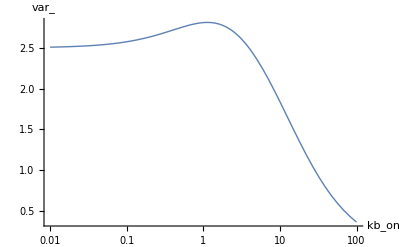

```mathematica
wb = c*kboff*kon / (c*kboff + kon);
wu = koff*ku / (c*kbon+koff+ku);
LogLinearPlot[{With[{dc =0.56, c =5.6, kbon = k, kboff=0.0888, koffu=5, konb=5, kuon=5}, Evaluate[var/pion^2]]},
{k,0.01,100}, AxesLabel->{kb_on,var_}, PlotStyle->{Thick}]
```

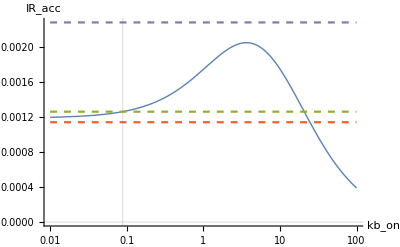

```mathematica
LogLinearPlot[{With[{dc =0.56, c =5.6, kbon = k, kboff=0.0888, koffu=5, konb=5, kuon=5}, Evaluate[IR]],
0,0.001259, 0.0011387, 0.0011387*2},
{k,0.01,100}, AxesLabel->{kb_on,IR_acc}, 
PlotStyle->{Thick, None,Dashed, Dashed, Dashed},
GridLines->{{0.0888,0}}]
```

```mathematica
0.25*0.01*5.6*0.0888*0.85*1.5
```

0.00158508

```mathematica
IRcdc = With[ {c=5.6, dc=0.56}, Evaluate[IR]];
```

```mathematica
NMaximize[{IRcdc, kbon <= 0.0001, kboff <= 0.0888,koffu <= 5, konb <=5, kuon<=5, kbon >= 10^-5, kboff >= 10^-5,koffu >= 10^-5, konb >= 10^-5, kuon>= 10^-5 }, {kbon, kboff, koffu, konb, kuon}]
```

{0.00118638,{kbon→0.0001,kboff→0.0888,koffu→5.,konb→5.,kuon→5.}}

```mathematica
(* Finding the first-passage time of a 3-state circuit *)
```

```mathematica
InverseLaplaceTransform[r*koff/(r*(koff+ku)*(r-c*kb+koff+ku)-ku), r, t]
```

```mathematica
FullSimplify[%]
```

(ⅇ^(-((-c kb (koff+ku)+(koff+ku)^2+√((koff+ku) (4 ku+(koff+ku) (-c kb+koff+ku)^2))) t)/(2 (koff+ku))) koff ((koff+ku) (-c kb+koff+ku)-ⅇ^((√((koff+ku) (4 ku+(koff+ku) (-c kb+koff+ku)^2)) t)/(koff+ku)) (koff+ku) (-c kb+koff+ku)+√((koff+ku) (4 ku+(koff+ku) (-c kb+koff+ku)^2))+ⅇ^((√((koff+ku) (4 ku+(koff+ku) (-c kb+koff+ku)^2)) t)/(koff+ku)) √((koff+ku) (4 ku+(koff+ku) (-c kb+koff+ku)^2))))/(2 (koff+ku) √((koff+ku) (4 ku+(koff+ku) (-c kb+koff+ku)^2)))

```mathematica
Q3off = {{-c*kb,0, c*kb},
               {0, 0, 0},
               {ku, koff, -(ku+koff)}};
```

```mathematica
P3off = MatrixExp[t*Q3off];
F3 = Dot[Q3off, P3off];
```

```mathematica
F3' = FullSimplify[F3][[3, 2]]
```

(ⅇ^(-1/2 (c kb+koff+ku+√(-4 c kb koff+(c kb+koff+ku)^2)) t) koff (-c kb+koff+ku-ⅇ^(√(-4 c kb koff+(c kb+koff+ku)^2) t) (-c kb+koff+ku)+√(-4 c kb koff+(c kb+koff+ku)^2)+ⅇ^(√(-4 c kb koff+(c kb+koff+ku)^2) t) √(-4 c kb koff+(c kb+koff+ku)^2)))/(2 √(-4 c kb koff+(c kb+koff+ku)^2))

```mathematica
FullSimplify[LaplaceTransform[F3', t, r]]
```

(koff (c kb+r))/(c kb (koff+r)+r (koff+ku+r))

```mathematica
(*comparing estimators*)
```